```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
GaussQ[g_,n_,a_,b_]:=Total[g[First[#]]*Last[#]&/@GaussianQuadratureWeights[n,a,b]]
```

6

{1+1/2 (-1-ξ),(1+ξ)/2}

{{Null,Null},{Null,Null}}

{{5.06667,-4.96667},{-4.96667,5.06667}}

{Null,Null}

{0.1,0.1}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{0,0,0,0,0,0}

6

0

0

0.2

0.2

{1,0}

{1,0}

{0,1}

{0,1}

{0.,0.0731972,0.109073,0.109073,0.0731972,0.}

{0.}

{0.,0.0731972,0.0731972,0.109073,0.109073,0.109073,0.109073,0.0731972,0.0731972,0.}

{}

{y[x]→-(ⅇ^-x (-1+ⅇ^x) (-ⅇ+ⅇ^x))/(1+ⅇ)}

-(ⅇ^-x (-1+ⅇ^x) (-ⅇ+ⅇ^x))/(1+ⅇ)

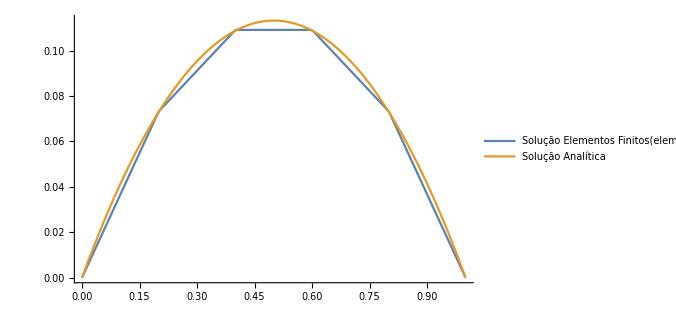

```mathematica
α=1;γ=1;
u0=0;u1=0;
n=5;h=1/n;np=4;m=n+1
φ={InterpolatingPolynomial[{{-1,1},{1,0}},ξ],InterpolatingPolynomial[{{-1,0},{1,1}},ξ]}
K={{,},{,}}
K=α*(2/h)*Table[GaussQ[D[φ[[r]],ξ]*D[φ[[s]],ξ]/.ξ->#&,np,-1,1],{r,2},{s,2}]+γ*(h/2)*Table[GaussQ[φ[[r]]*φ[[s]]/.ξ->#&,np,-1,1],{r,2},{s,2}]
F={,}

F=(h/2)*Table[GaussQ[φ[[r]]/.ξ->#&,np,-1,1],{r,2}]
K1=ConstantArray[0,{n+1,n+1}]
For[i=1,i<m,i=i+1,
K1[[i;;i+1,i;;i+1]]=K1[[i;;i+1,i;;i+1]]+K

]
F1=ConstantArray[0,{n+1}]
For[i=1,i<m,i=i+1,
F1[[i;;i+1]]=F1[[i;;i+1]]+F

]
m=n+1
F1[[1]]=u0
F1[[m]]=u1
F1[[2]]=F1[[2]]-K1[[2,1]]*u0
F1[[m-1]]=F1[[m-1]]-K1[[m-1,m]]*u1
K1[[1,1;;2]]={1,0}
K1[[1;;2,1]]={1,0}
K1[[m,m-1;;m]]={0,1}
K1[[m-1;;m,m]]={0,1}

w=LinearSolve[K1,F1]
LagrangeP[p1_]:={Piecewise[{{InterpolatingPolynomial[{{p1,1},{p1+h,0}},x],p1<=x≤p1+h}},0],Piecewise[{{InterpolatingPolynomial[{{p1,0},{p1+h,1}},x],p1<=x≤p1+h}},0]}
W1={w[[1]]}
For[i=2,i<m,i++,
W1=Join[W1,ConstantArray[w[[i]],{2}]]
]
W1=Join[W1,{w[[m]]}]
ϕ={}
For[i=1,i<=n,i++,
AppendTo[ϕ,LagrangeP[(i-1)*h][[1]]];
AppendTo[ϕ,LagrangeP[(i-1)*h][[2]]]
]

Uh[x_]:=W1.ϕ
solution=DSolve[{-α*y''[x]+γ*y[x]==1,y[0]==0,y[1]==0},y[x],x][[1]]
u[x_]=y[x]/.solution[[1]]
Plot[{Uh[x],u[x]},{x,0,1},PlotRange->All,ImageSize->500,AxesStyle->Black,ImageSize->400,PlotLegends->{"Solução Elementos Finitos(elementos lineares)","Solução Analítica"}]
```